This is an example of how to use the Cosmology.m package. It provides basic functions commonly used in cosmological computations, but no power spectra or anything more advanced. So far it’s LCDM only but it could be easily extended. Feel free to evaluate the entire notebook at once.

First, load the package.

```mathematica
Get[NotebookDirectory[]<>"Cosmology.m"]
```

Show all functions of this package.

```mathematica
?Cosmology`*
```

Compute comoving distance at z=1. The Distance function is being memoized in interpolated form, so the first call takes longer then subsequent calls.

```mathematica
AbsoluteTiming[Distance[1.]]
```

```mathematica
AbsoluteTiming[Distance[1.]]
```

Change to Luminosity distance.

```mathematica
Distance[1.,DistanceType->Luminosity]
```

Vary a cosmological parameter.

```mathematica
Plot[Evaluate@Table[Distance[z,OmegaM->x],{x,{.1,.2,.25,.3,.4}}],{z,0,3}]
```

Show the fiducial model.

```mathematica
Cosmology
```

Copy and paste the previous output to define your own model (LCDM only). In this case, we set h -> .73 instead of .7 and OmegaK->1.1 instead of 1. We also change the dependency, i.e. make OmegaTot depend on OmegaK instead of the other way around.

```mathematica
Cosmology={OmegaM->0.25,OmegaB->0.05,OmegaC->-OmegaB+OmegaM,OmegaL->0.75,OmegaTot->1-OmegaK,OmegaK->1.1,h->0.73,H0->0.0003333333333333333 h,omegaM->h^2 OmegaM,omegaL->h^2 OmegaL,omegaB->h^2 OmegaB,omegaC->h^2 OmegaC,omegaK->h^2 OmegaK,w0->-1,w1->0,gamma->0.545,sigma8->0.8,ns->0.9};
```

```mathematica
Distance[1.]
```

This is how you use the power spectrum and non-linear corrections

```mathematica
Omega21[a_,k_]:=-1.5 * Fiducial@OmegaM/(a^3*  Fiducial@OmegaL + Fiducial@ OmegaM);
Omega22[a_,k_]:=2-(-2*a^3 Fiducial@OmegaL+ Fiducial@OmegaM)/(2(a^3 Fiducial@OmegaL+ Fiducial@OmegaM));
```

InterpolatingFunction::dmval: Input value {-4.60508} lies outside the range of data in the interpolating function. Extrapolation will be used.

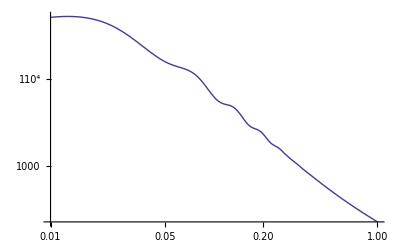

```mathematica
LogLogPlot[NonlinearPowerSpectrumHalofit[k,PowerSpectrum[#,0]&],{k,.01,1}]
```

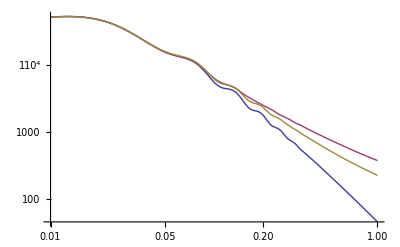

```mathematica
Quiet@LogLogPlot[{PowerSpectrum[k,0],NonlinearPowerSpectrumTRG[k,PowerSpectrum[#,0]&,Omega21,Omega22],NonlinearPowerSpectrumHalofit[k,PowerSpectrum[#,0]&]},{k,.01,1}]
```